{{2,150},{3,188},{4,246},{5,282},{6,362},{7,436},{8,540},{9,632},{10,750},{11,870},{12,990},{13,1115},{14,1270},{15,1440},{16,1608},{17,1780},{18,1950}}

{{150,2},{188,3},{246,4},{282,5},{362,6},{436,7},{540,8},{632,9},{750,10},{870,11},{990,12},{1115,13},{1270,14},{1440,15},{1608,16},{1780,17},{1950,18}}

93.8676+16.2393 x+4.86365 x^2

100+15 x+5 x^2

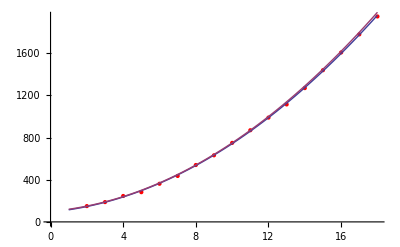

0.731321+0.0145015 x-3.0165×10^-6 x^2

0.72+0.0145 x-3.×10^-6 x^2

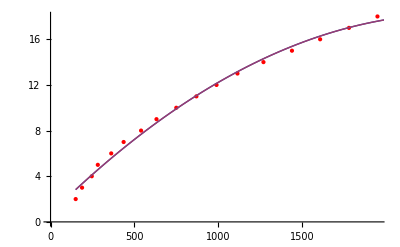

0.

```mathematica
data = { (* level,game-time (seconds) *)
{2,150},
{3,188},
{4,246},
{5,282},
{6,362},
{7,436},
{8,540},
{9,632},
{10,750},
{11,870},
{12,990},
{13,1115},
{14,1270},
{15,1440},
{16,1608},
{17,1780},
{18,1950}
}
data2 = {#[[2]],#[[1]]}& /@ data
parabola = Fit[data, {1,x,x^2}, x]
para2 = 100+15x+5 x^2
Show[ListPlot[data,PlotStyle->Red],Plot[{parabola,para2},{x,1,18}]]

parabola2 = Fit[data2, {1,x, x^2}, x]
parabola3 =0.72 +0.0145 x-3.0*^-6 x^2
Show[ListPlot[data2,PlotStyle->Red],Plot[{parabola3,parabola3},{x,150,2000}]]

levelAt[t_/; t > 100] := 1/10 (-15+Sqrt[5] Sqrt[-355+4 t])
levelAt[t_]:=1
timeAt[lv_] := 100+15lv+5 lv^2
timeAt[1] := 0
timeAt[1]/60.0
```

1/30

70

180

90

{{1,475},{2,1138.},{3,1334.},{4,1697.},{5,2051.},{6,2455.},{7,3005.},{8,3577.},{9,4175.},{10,4924.},{11,5730.},{12,6537.},{13,7537.},{14,8536.},{15,9601.},{16,10843.},{17,12124.},{18,13444.}}

989.712+38.5814 x^2

1048+38 x^2

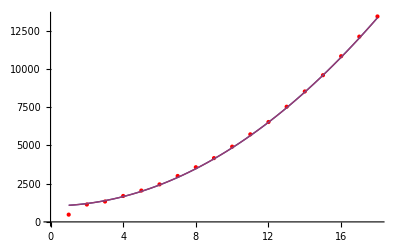

```mathematica
wavesPerSecond = 1/30
siege2Wave = (35*60) wavesPerSecond
upgradeCycle = 180 (*seconds*)
firstWaveAt = 90 (*seconds*)
cycle[t_] := Floor[t / upgradeCycle]
minionCaster[t_] := 16.5 + 0.5 cycle[t]
minionMelee[t_] := 22.5 + 0.5 cycle[t]
minionSiege[t_] := 27 + 1 cycle[t]
Clear[waveGold]
waveGold[t_,w_Integer/; w ≤ 0] := 0
waveGold[t_,w_Integer] := waveGold[t-30,w-1] + 3 minionCaster[t] + 3 minionMelee[t] + Boole@(Mod[w,If[w ≥ siege2Wave,2,3]]==0)minionSiege[t]

minionGoldAt[t_] := waveGold[t,Floor[(t-60) wavesPerSecond]]
(* TODO: make sure this is right *)
passiveGoldAt[t_] := (t/10)*19 (*summoner's rift*)
exactGoldAtTime[t_] := minionGoldAt[t] + passiveGoldAt[t] + 475
data = {#,exactGoldAtTime[timeAt[#]]}& /@ Range[1,18]

parabola = Fit[data, {1, x^2}, x]
parabola2 = 1048 + 38 x^2 
Show[ListPlot[data,PlotStyle->Red],Plot[{parabola2,parabola2},{x,1,18}]]

goldAtLV[lv_]:= 1048 + 38 lv^2
```

60

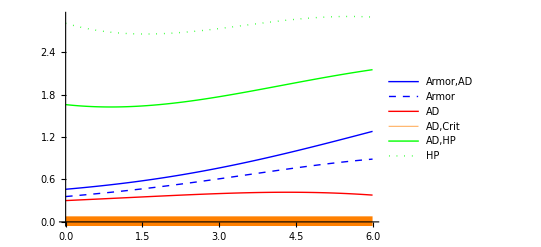

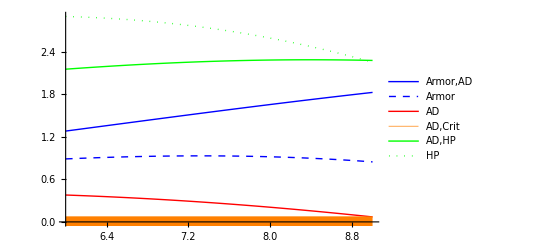

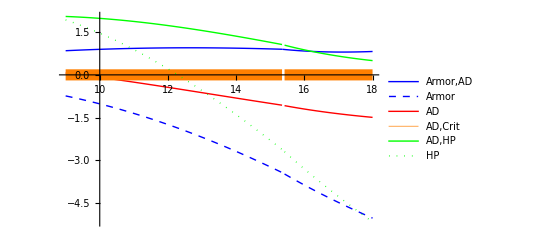

```mathematica
armor[x_,r_] := (100/(100+(x*r)))
hp[x_] := (baseHP + x) / baseHP
attack[x_] := (baseAD+x) / baseAD
crit[x_] := 1 + (1 *Min[1,x])


(*curv[x_]:= Abs[armor''[x]] / (1+(armor'[x]^2))^(3/2)*)


hitenStyle[aspd_] := {45*6 *aspd,False,15}
bladeSurge [ad_]:= {20+ad,True, 14}
equilibriumStrike[ap_] := {80 +(ap*0.5), True, 8}

enemyResist = 60
abilities[ad_] := {hitenStyle[1],bladeSurge[ad], equilibriumStrike[0]}
abilityDmg[ad_, d_] := Module[{dmg},
dmg[f_,dur_] := With[{
x= 1+Floor[(dur/f⟦3⟧)],
scale = If[f⟦2⟧,enemyResist, 1]
}, (scale*f⟦1⟧*x)];
Total[Map[dmg[#,d]&, abilities[ad]]]
]

abilityDPS[ad_, resist_] := Total[(If[#⟦2⟧,resist, 1]*(#⟦1⟧/#⟦3⟧)&) /@ abilities[ad]]

dps[ad_, cc_, resist_] := resist * ad * crit[cc] 

totalDPS[ad_,cc_, ar_, armorReduction_] := With[
{x=armor[ar,armorReduction ]},
abilityDPS[ad,x] + dps[ad,cc, x]]

critCapRedistro[ad_,cc_, goldCrit_] := If[cc > 1,ad+((goldCrit-5000)/36), ad];

metric[lv_, goldScale_, armorReduction_] := Module[{
baseHP = 456 + 90 lv,
baseAD = 56 + 3.3lv,
baseArmor = 15 + 3.75 lv,
goldAD, goldCrit, goldHP, goldArmor,

totalGold,dur, totalDamage, enemyDPS,selfDPS,cc,hp, ad, ar, enemyCritGold, enemyCC, enemyAD, enemyHP
},
totalGold = goldAtLV[lv];
{goldAD, goldCrit, goldHP, goldArmor} = goldScale * totalGold;
cc = (goldCrit / 50)/100;
hp = baseHP +(goldHP / 2.64);
ar = baseArmor + (goldArmor / 20);
ad = baseAD + critCapRedistro[goldAD / 36, cc,goldCrit];
enemyCritGold = totalGold/2;
enemyCC = enemyCritGold/50/100;
enemyAD = baseAD + critCapRedistro[(totalGold/2) / 36, enemyCC,enemyCritGold];
enemyHP = baseHP;
enemyDPS =totalDPS[enemyAD,enemyCC, ar, armorReduction];
selfDPS = totalDPS[ad,cc, baseArmor, armorReduction];
(hp/enemyDPS ) - (enemyHP/selfDPS)
(*
dur= hp/enemyDPS;
totalDamage = dur*(totalDPS[ad,cc, baseArmor, armorReduction]);
(hp -(enemyDPS*dur)) -(enemyHP-totalDamage) *)
]

xs[lv_, r_] :={ 
	metric[lv, {1/2, 0, 0, 1/2}, r], 
	metric[lv,{0, 0, 0, 1}, r],
	metric[lv,{1,0,0,0}, r],
	metric[lv,{1 /2,1 /2, 0, 0}, r],
	metric[lv,{1/2, 0, 1/2, 0}, r],
	metric[lv,{0,0,1,0}, r]
};


plot[a_,b_] := Plot[a, b, PlotLegends->{"Armor,AD","Armor", "AD","AD,Crit","AD,HP", "HP"}, PlotStyle-> 
{Blue,
Directive[Dashed,Blue,Thick],
Red,
Directive[Orange,Thickness[0.02]],
Green, 
Directive[Dotted,Green,Thick]}]

plot[xs[x,0.94], {x,0,6}]
plot[xs[ x,0.94], {x,6,9}]
plot[xs[ x, 0.65], {x,9,18}]
```

```mathematica
"hmm"
goldAtLV[18]
 
lv = 18
baseHP = 456 + 90 lv
baseAD = 56 +3.3 lv
baseArmor = 15 +3.75 lv
totalGold = goldAtLV[lv]
enemyCritGold = totalGold/2
enemyCC = enemyCritGold/50/100.0
enemyAD = baseAD + critCapRedistro[(totalGold/2) / 36, enemyCC,enemyCritGold]
enemyDPS =totalDPS[enemyAD,enemyCC, baseArmor, 0.94]
enemyHP = baseHP

hp = baseHP +((totalGold/2) / 2.64);
ar = baseArmor + (0 / 20);
ad = baseAD + critCapRedistro[(totalGold/2) / 36, 0,0]
selfDPS = totalDPS[ad,0, baseArmor, 0.94]
{hp, enemyDPS,hp/enemyDPS }
{enemyHP, selfDPS, enemyHP/selfDPS}
(hp/enemyDPS ) -  (enemyHP/selfDPS)
(*
Plot3D[{
(y*armor[x,armorReduction])/baseAD,
(y+ads[x])/baseAD,
(y*crit[x])/baseAD}, {x,0,15000},{y,0,200},  PlotStyle->{Blue,Red,Green}]
Maximize[{armor''[x], {x >= 0, x <= 500}}, x, Reals]
*)
```

hmm

13360

18

2076

115.4

82.5

13360

6680

1.336

347.622

429.998

2076

300.956

206.049

{4606.3,429.998,10.7124}

{2076,206.049,10.0753}

0.637098